# Quartic Double-well Potential

## Units

Unit conversion factors:

```mathematica
bohr2a=0.529177`50;
a2bohr=1/bohr2a;
au2kcal=627.5095`50;
kcal2au=1/au2kcal;
ev2cm=8065.54477`50;
cm2ev = 1/ev2cm ;
au2ev=27.2113`50;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`50*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

Physical constants:

```mathematica
hbar=1;
hbarps=0.047685388`50/(au2kcal*π);
Dalton=1822.8900409014022`50;
MassH=1.0072756064562605`50;
MassD=2.0135514936645316`50;
MassT=3.0160492`50;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`50*10^-6;
```

## Potential:

```mathematica
U4[f_,Ub_,x_,OptionsPattern[{M->MassH}]]:=Module[{m,ω,Vb,λ2,a2},
m=OptionValue[M]Dalton;
ω=f*cm2au;
Vb=Ub*kcal2au;
a2=(8 Vb)/(m ω^2);
λ2=1/2(m ω^2)/a2;
au2kcal λ2/4(x^2-a2)^2
];
```

```mathematica
3000.0/Sqrt[2.0]
```

2121.32

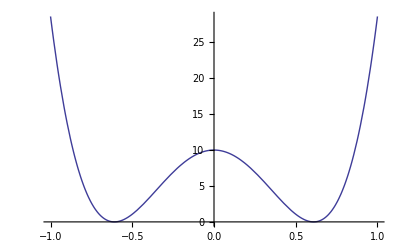

```mathematica
Plot[U4[3000,7,x],{x,-1,1}]
```

```mathematica
Table[{x,U4[3000,7,x]},{x,-1.5,1.5,0.01}]//TableForm
```

-1.5 | 409.623
-1.49 | 397.406
-1.48 | 385.453
-1.47 | 373.761
-1.46 | 362.327
-1.45 | 351.147
-1.44 | 340.217
-1.43 | 329.534
-1.42 | 319.094
-1.41 | 308.893
-1.4 | 298.928
-1.39 | 289.196
-1.38 | 279.693
-1.37 | 270.416
-1.36 | 261.361
-1.35 | 252.525
-1.34 | 243.904
-1.33 | 235.495
-1.32 | 227.295
-1.31 | 219.301
-1.3 | 211.509
-1.29 | 203.916
-1.28 | 196.519
-1.27 | 189.315
-1.26 | 182.3
-1.25 | 175.471
-1.24 | 168.825
-1.23 | 162.36
-1.22 | 156.072
-1.21 | 149.957
-1.2 | 144.014
-1.19 | 138.239
-1.18 | 132.629
-1.17 | 127.18
-1.16 | 121.891
-1.15 | 116.759
-1.14 | 111.779
-1.13 | 106.95
-1.12 | 102.269
-1.11 | 97.7334
-1.1 | 93.3396
-1.09 | 89.0852
-1.08 | 84.9675
-1.07 | 80.9839
-1.06 | 77.1316
-1.05 | 73.4081
-1.04 | 69.8107
-1.03 | 66.3367
-1.02 | 62.9837
-1.01 | 59.7491
-1. | 56.6304
-0.99 | 53.6251
-0.98 | 50.7306
-0.97 | 47.9447
-0.96 | 45.2647
-0.95 | 42.6884
-0.94 | 40.2134
-0.93 | 37.8373
-0.92 | 35.5579
-0.91 | 33.3727
-0.9 | 31.2796
-0.89 | 29.2762
-0.88 | 27.3605
-0.87 | 25.5301
-0.86 | 23.7829
-0.85 | 22.1168
-0.84 | 20.5296
-0.83 | 19.0192
-0.82 | 17.5836
-0.81 | 16.2207
-0.8 | 14.9284
-0.79 | 13.7049
-0.78 | 12.5481
-0.77 | 11.456
-0.76 | 10.4268
-0.75 | 9.45855
-0.74 | 8.54934
-0.73 | 7.69736
-0.72 | 6.90077
-0.71 | 6.15777
-0.7 | 5.46658
-0.69 | 4.82547
-0.68 | 4.23269
-0.67 | 3.68656
-0.66 | 3.18539
-0.65 | 2.72754
-0.64 | 2.31137
-0.63 | 1.93529
-0.62 | 1.59772
-0.61 | 1.2971
-0.6 | 1.03192
-0.59 | 0.800663
-0.58 | 0.60186
-0.57 | 0.434056
-0.56 | 0.295823
-0.55 | 0.185758
-0.54 | 0.102485
-0.53 | 0.0446485
-0.52 | 0.0109215
-0.51 | 6.56631×10^-8
-0.5 | 0.0106057
-0.49 | 0.0414846
-0.48 | 0.0914077
-0.47 | 0.159171
-0.46 | 0.243595
-0.45 | 0.343525
-0.44 | 0.457831
-0.43 | 0.58541
-0.42 | 0.72518
-0.41 | 0.876086
-0.4 | 1.0371
-0.39 | 1.20721
-0.38 | 1.38544
-0.37 | 1.57084
-0.36 | 1.76247
-0.35 | 1.95943
-0.34 | 2.16083
-0.33 | 2.36582
-0.32 | 2.57357
-0.31 | 2.78326
-0.3 | 2.99413
-0.29 | 3.2054
-0.28 | 3.41636
-0.27 | 3.62628
-0.26 | 3.8345
-0.25 | 4.04034
-0.24 | 4.24318
-0.23 | 4.44241
-0.22 | 4.63744
-0.21 | 4.82772
-0.2 | 5.01271
-0.19 | 5.19191
-0.18 | 5.36482
-0.17 | 5.531
-0.16 | 5.69
-0.15 | 5.84142
-0.14 | 5.98486
-0.13 | 6.11998
-0.12 | 6.24644
-0.11 | 6.36392
-0.1 | 6.47214
-0.09 | 6.57084
-0.08 | 6.65979
-0.07 | 6.73876
-0.06 | 6.80759
-0.05 | 6.8661
-0.04 | 6.91415
-0.03 | 6.95165
-0.02 | 6.97849
-0.01 | 6.99462
0. | 7.
0.01 | 6.99462
0.02 | 6.97849
0.03 | 6.95165
0.04 | 6.91415
0.05 | 6.8661
0.06 | 6.80759
0.07 | 6.73876
0.08 | 6.65979
0.09 | 6.57084
0.1 | 6.47214
0.11 | 6.36392
0.12 | 6.24644
0.13 | 6.11998
0.14 | 5.98486
0.15 | 5.84142
0.16 | 5.69
0.17 | 5.531
0.18 | 5.36482
0.19 | 5.19191
0.2 | 5.01271
0.21 | 4.82772
0.22 | 4.63744
0.23 | 4.44241
0.24 | 4.24318
0.25 | 4.04034
0.26 | 3.8345
0.27 | 3.62628
0.28 | 3.41636
0.29 | 3.2054
0.3 | 2.99413
0.31 | 2.78326
0.32 | 2.57357
0.33 | 2.36582
0.34 | 2.16083
0.35 | 1.95943
0.36 | 1.76247
0.37 | 1.57084
0.38 | 1.38544
0.39 | 1.20721
0.4 | 1.0371
0.41 | 0.876086
0.42 | 0.72518
0.43 | 0.58541
0.44 | 0.457831
0.45 | 0.343525
0.46 | 0.243595
0.47 | 0.159171
0.48 | 0.0914077
0.49 | 0.0414846
0.5 | 0.0106057
0.51 | 6.56631×10^-8
0.52 | 0.0109215
0.53 | 0.0446485
0.54 | 0.102485
0.55 | 0.185758
0.56 | 0.295823
0.57 | 0.434056
0.58 | 0.60186
0.59 | 0.800663
0.6 | 1.03192
0.61 | 1.2971
0.62 | 1.59772
0.63 | 1.93529
0.64 | 2.31137
0.65 | 2.72754
0.66 | 3.18539
0.67 | 3.68656
0.68 | 4.23269
0.69 | 4.82547
0.7 | 5.46658
0.71 | 6.15777
0.72 | 6.90077
0.73 | 7.69736
0.74 | 8.54934
0.75 | 9.45855
0.76 | 10.4268
0.77 | 11.456
0.78 | 12.5481
0.79 | 13.7049
0.8 | 14.9284
0.81 | 16.2207
0.82 | 17.5836
0.83 | 19.0192
0.84 | 20.5296
0.85 | 22.1168
0.86 | 23.7829
0.87 | 25.5301
0.88 | 27.3605
0.89 | 29.2762
0.9 | 31.2796
0.91 | 33.3727
0.92 | 35.5579
0.93 | 37.8373
0.94 | 40.2134
0.95 | 42.6884
0.96 | 45.2647
0.97 | 47.9447
0.98 | 50.7306
0.99 | 53.6251
1. | 56.6304
1.01 | 59.7491
1.02 | 62.9837
1.03 | 66.3367
1.04 | 69.8107
1.05 | 73.4081
1.06 | 77.1316
1.07 | 80.9839
1.08 | 84.9675
1.09 | 89.0852
1.1 | 93.3396
1.11 | 97.7334
1.12 | 102.269
1.13 | 106.95
1.14 | 111.779
1.15 | 116.759
1.16 | 121.891
1.17 | 127.18
1.18 | 132.629
1.19 | 138.239
1.2 | 144.014
1.21 | 149.957
1.22 | 156.072
1.23 | 162.36
1.24 | 168.825
1.25 | 175.471
1.26 | 182.3
1.27 | 189.315
1.28 | 196.519
1.29 | 203.916
1.3 | 211.509
1.31 | 219.301
1.32 | 227.295
1.33 | 235.495
1.34 | 243.904
1.35 | 252.525
1.36 | 261.361
1.37 | 270.416
1.38 | 279.693
1.39 | 289.196
1.4 | 298.928
1.41 | 308.893
1.42 | 319.094
1.43 | 329.534
1.44 | 340.217
1.45 | 351.147
1.46 | 362.327
1.47 | 373.761
1.48 | 385.453
1.49 | 397.406
1.5 | 409.623